# Fresnel

```mathematica
<<"Labor`"
```

## Messung

### Laser auf 45° einstellen damit s und p Polaritierung gleich sind

### Optische Achse einrichten

### Justieren des Sschwenkarms ~90° zum festem Arm

### Messen der reflektierten intsensität

```mathematica
dI=0.004;
dα=1 Degree;
off= 0.001;
(*p=0
s=90*)
Ir={{"α/°", "I l-g p/V", "I l-g s/V", "I g-l p/V", "I g-l s/V"}, {15, 0.079, 0.099, 0.051, 0.090}, {20, 0.074, 0.108, 0.039, 0.108}, {25, 0.067, 0.119, 0.024, 0.144}, {26, □, □, 0.021, □}, {27, □, □, 0.018, □}, {28, □, □, 0.014, □}, {29, □, □, 0.010, □}, {30, 0.056, 0.135, 0.006, 0.194}, {31, □, □, 0.005, □}, {32, □, □, 0.003, □}, {33, □, □, 0.003, □}, {34, □, □, 0.004, □}, {35, 0.045, 0.155, 0.010, 0.354}, {36, □, □, 0.017, 0.404}, {37, □, □, 0.038, 0.480}, {38, □, □, 0.082, 0.598}, {39, □, □, 0.148, 0.717}, {40, 0.033, 0.180, 0.381, 1.085}, {41, □, □, 1.200, 1.708}, {42, □, □, 1.903, 1.966}, {43, □, □, 1.910, 1.973}, {44, □, □, 1.930, 1.975}, {45, 0.020, 0.218, 1.885, 1.940}, {50, 0.008, 0.268, 1.841, 1.888}, {51, 0.007, □, □, □}, {52, 0.005, □, □, □}, {53, 0.004, □, □, □}, {54, 0.003, □, □, □}, {55, 0.002, 0.338, 1.853, 1.880}, {56, 0.002, □, □, □}, {57, 0.003, □, □, □}, {58, 0.003, □, □, □}, {59, 0.005, □, □, □}, {60, 0.008, 0.430, 1.815, 1.896}, {65, 0.036, 0.556, 1.914, 1.970}, {66, 0.049, □, □, □}, {67, 0.061, □, □, □}, {68, 0.075, □, □, □}, {69, 0.093, □, □, □}, {70, 0.111, 0.734, 1.923, 1.982}, {71, 0.136, □, □, □}, {72, 0.162, □, □, □}, {73, 0.201, □, □, □}, {74, 0.241, □, □, □}, {75, 0.275, 0.989, 1.970, 2.076}, {76, 0.333, □, □, □}, {77, 0.394, □, □, □}, {78, 0.456, □, □, □}, {79, 0.525, □, □, □}, {80, 0.605, 1.315, 1.797, 2.063}, {81, 0.705, □, □, □}, {82, 0.800, □, □, □}, {83, 0.905, □, □, □}, {84, 1.054, □, □, □}, {85, 1.173, 1.692, 1.953, 2.024}};Ir1={{"α/°", "I l-g p/V"}, {15, 0.079}, {20, 0.074}, {25, 0.067}, {30, 0.056}, {35, 0.045}, {40, 0.033}, {45, 0.020}, {50, 0.008}, {51, 0.007}, {52, 0.005}, {53, 0.004}, {54, 0.003}, {55, 0.002}, {56, 0.002}, {57, 0.003}, {58, 0.003}, {59, 0.005}, {60, 0.008}, {65, 0.036}, {66, 0.049}, {67, 0.061}, {68, 0.075}, {69, 0.093}, {70, 0.111}, {71, 0.136}, {72, 0.162}, {73, 0.201}, {74, 0.241}, {75, 0.275}, {76, 0.333}, {77, 0.394}, {78, 0.456}, {79, 0.525}, {80, 0.605}, {81, 0.705}, {82, 0.800}, {83, 0.905}, {84, 1.054}, {85, 1.173}};Ir2={{"α/°", "I l-g s/V"}, {15, 0.099}, {20, 0.108}, {25, 0.119}, {30, 0.135}, {35, 0.155}, {40, 0.180}, {45, 0.218}, {50, 0.268}, {55, 0.338}, {60, 0.430}, {65, 0.556}, {70, 0.734}, {75, 0.989}, {80, 1.315}, {85, 1.692}};Ir3={{"α/°", "I g-l p/V"}, {15, 0.051}, {20, 0.039}, {25, 0.024}, {26, 0.021}, {27, 0.018}, {28, 0.014}, {29, 0.010}, {30, 0.006}, {31, 0.005}, {32, 0.003}, {33, 0.003}, {34, 0.004}, {35, 0.010}, {36, 0.017}, {37, 0.038}, {38, 0.082}, {39, 0.148}, {40, 0.381}, {41, 1.200}, {42, 1.903}, {43, 1.910}, {44, 1.930}, {45, 1.885}, {50, 1.841}, {55, 1.853}, {60, 1.815}, {65, 1.914}, {70, 1.923}, {75, 1.970}, {80, 1.797}, {85, 1.953}};Ir4={{"α/°", "I g-l s/V"}, {15, 0.090}, {20, 0.108}, {25, 0.144}, {30, 0.194}, {35, 0.354}, {36, 0.404}, {37, 0.480}, {38, 0.598}, {39, 0.717}, {40, 1.085}, {41, 1.708}, {42, 1.966}, {43, 1.973}, {44, 1.975}, {45, 1.940}, {50, 1.888}, {55, 1.880}, {60, 1.896}, {65, 1.970}, {70, 1.982}, {75, 2.076}, {80, 2.063}, {85, 2.024}};
```

### Normierung der Intensität

```mathematica
I0={{"I l-g/V", "I g-l/V"}, {2.525, 2.221}};
```

### Graphische Darstellung

```mathematica
<<ErrorBarPlots`
```

```mathematica
pIs=Table[{Ir4[[x,1]],(Ir4[[x,2]]-off)/I0[[2,2]]},{x,2,Length[Ir4]}];
pIp=Table[{Ir3[[x,1]],(Ir3[[x,2]]-off)/I0[[2,2]]},{x,2,Length[Ir3]}];
pIp2=Table[{Ir1[[x,1]],(Ir1[[x,2]]-off)/I0[[2,1]]},{x,2,Length[Ir1]}];
pIs2=Table[{Ir2[[x,1]],(Ir2[[x,2]]-off)/I0[[2,1]]},{x,2,Length[Ir2]}];
```

```mathematica
<<PlotLegends`
ListLogPlot[{pIs,pIp,pIp2,pIs2},PlotLegend->{Ir4[[1,2]],Ir3[[1,2]],Ir1[[1,2]],Ir2[[1,2]]},AxesLabel->{"α/°","I/V"}]
```

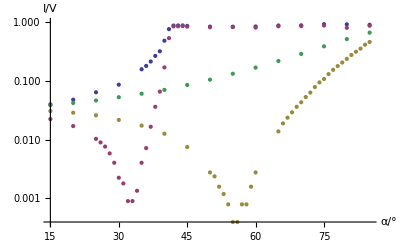

### Berechnen der Brechzahl

```mathematica
n1=1;dn1=0;
α=41.3Degree;dα=0.1Degree;
n2=Optic`RefIndexTotal[n1,dn1,α,dα]//N
```

{1.51515,0.00301009}

### Berechnen der theoretischen p und s Reflextion

```mathematica
ArcSin[(n1 Ir[[6,1]]Degree)/n2[[1]]]*180/π
```

18.1206

```mathematica
Ist=Table[Optic`Fresnel[n1,n2[[1]],x Degree,ArcSin[(n1 Sin[x Degree])/n2[[1]]],dn1,n2[[2]],dα,dα],{x,0,90}];
Ipt=Table[Optic`Fresnel[n2[[1]],n1,x Degree,ArcSin[(n1 Sin[x Degree])/n2[[1]]],n2[[2]],dn1,dα,dα],{x,0,90}];
Ist2=Table[Optic`Fresnel[n1,n2[[1]],x Degree,ArcSin[(n2[[1]]Sin[x Degree])/n1],dn1,n2[[2]],dα,dα],{x,0,90}];
Ipt2=Table[Optic`Fresnel[n2[[1]],n1,x Degree,ArcSin[(n2[[1]] Sin[x Degree])/n1],n2[[2]],dn1,dα,dα],{x,0,90}];
```

Part::partw: Part 92 of {{0.20481806651236695`, 0.0009516625295390426`}, {0.20491263427638112`, 0.000988331505631895`}, {0.20519676971419704`, 0.0010249629133383224`}, {0.20567177433286155`, 0.00106159581424085`}, {0.20633983432816963`, 0.001098269133454459`}, {0.207204046529486`, 0.0011350218681531543`}, « 40 », {0.7099650392393858`  - 0.7042369225323375` ⅈ, 0.005762370998774379`}, {0.6482054484909666`  - 0.7614654926827774` ⅈ, 0.006022806094383005`}, {0.5865964386242469`  - 0.809879384966274` ⅈ, 0.006254251936762869`}, {0.5252130707276099`  - 0.8509707576273547` ⅈ, 0.006461429662073882`}, « 41 »} does not exist.

Part::partw: Part 92 of {{0.20481806651236695`, 0.0009516625295390426`}, {0.20477688306307873`, 0.0009759039708370288`}, {0.20465327046527276`, 0.0010001912840631657`}, {0.2044470417982271`, 0.0010245368623817445`}, {0.20415788495706105`, 0.0010489531554646173`}, {0.20378536179482531`, 0.0010734526926137807`}, {0.203328906916628`, 0.0010980481059683802`}, « 38 », {0.09558847702554847`, 0.0023052289723621954`}, {0.0892040131459782`, 0.0023489108155556266`}, {0.08251957991860781`, 0.002393712653463986`}, {0.07552035070487534`, 0.0024396894657681694`}, {0.06819057248628878`, 0.0024868991853940654`}, « 41 »} does not exist.

Part::partw: Part 92 of {{-0.20481806651236695`, 0.0009516625295390426`}, {-0.20472349492438618`, 0.000988411436104285`}, {-0.20443930197974614`, 0.0010252949246647568`}, {-0.20396404695558565`, 0.0010623712513427716`}, {-0.20329530788801586`, 0.0010996997442014693`}, {-0.20242964987880124`, 0.0011373412715718866`}, « 40 », {0.05602879397684529`  - 0.9984291533431403` ⅈ, 0.008169579034378429`}, {-0.0587605518586829` - 0.9982721059637311` ⅈ, 0.007895826378774135`}, {-0.15724907693096718` - 0.9875589743424737` ⅈ, 0.007626373436096507`}, {-0.24258055607522733` - 0.9701312662801016` ⅈ, 0.00736621662244301`}, « 41 »} does not exist.

General::stop: Further output of Part will be suppressed during this calculation.

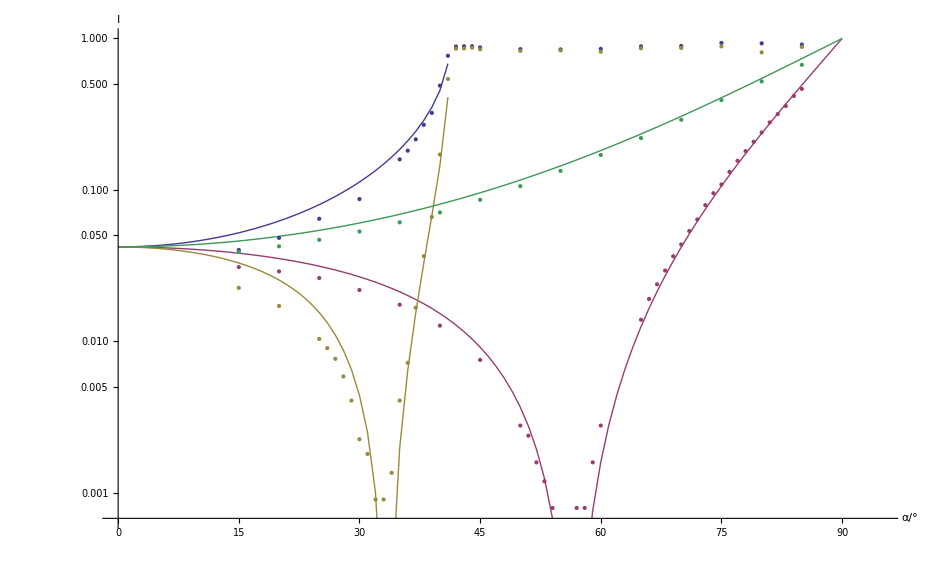

```mathematica
Show[ListLogPlot[{
Table[{x,Ipt2[[x+1,1]]^2},{x,0,Length[Ipt2]}],
Table[{x,Ipt[[x+1,1]]^2},{x,0,Length[Ipt]}],
Table[{x,Ist2[[x+1,1]]^2},{x,0,Length[Ist2]}],
Table[{x,Ist[[x+1,1]]^2},{x,0,Length[Ist]}]
},PlotRange->{{0,95},{-1,1}},Joined-> True],
ListLogPlot[{pIs,pIp2,pIp,pIs2}],AxesLabel->{"α/°","I"}]
```